Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Indeterminate

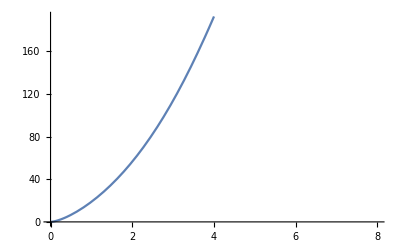

```mathematica
MyPy[R_,L_,l_,H_]:=Module[{Vs,Vk},
If[H<0,"Mahutis pole vett",If[H>2*R,"Vedeliku kõrgus ületab mahuti diameetri",Vs=π*R^2*L-L*(R^2*ArcSin[1]-R^2*ArcSin[(H-R)/R]-(H-R)*Sqrt[2*H*R-H^2]);If[H≤ R,d=R-H;If[d==0,Vk=H/(3*R)*(R^3*ArcCos[d/R]-2*R*d*Sqrt[R^2-d^2]+0 )],Vk=H/(3*R)*(R^3*ArcCos[d/R]-2*R*d*Sqrt[R^2-d^2]+d^3*Log[(R+Sqrt[R^2-d^2])/d]);N[Vs+2*Vk]],d=H-R;Vk=H/(3*R)*(R^3*ArcCos[d/R]-2*R*d*Sqrt[R^2-d^2]+0 );N[Vs+2*(π*R^2*l/3-Vk)]]]
]]
]

MyPy[4,5,6,4]
Plot[MyPy[4,5,6,h],{h,0,8}]
```